# xAct Amplitude Calculations

```mathematica
$HistoryLength=0;
```

```mathematica
(* Some Settings *)
TargetNucleonType="Proton"; (* accepts PROTON or NEUTRON *)
PionType="Neutral"; (* accepts PLUS, MINUS, or NEUTRAL*)
useEnergyDependentWidth=False; (* Accepts TRUE/FALSE *)

SaveResults=True;
```

```mathematica
mProton=0.938272; (* mass of Proton in GeV/c^2 *)
mNeutron=0.939565; (* mass of Neutron in GeV/c^2 *)
mπCharged=0.139570; (* mass of π^± in GeV/c^2 *)
mπNeutral=0.134977; (* mass of π^0 in GeV/c^2 *)
me=0.000511; (* mass of electron in GeV/c^2 *)
mR=1.440; (* mass of Roper resonance in GeV/c^2 *)
ΓR=0.350; (* width of Roper resonance in GeV/c^2 *)

(* Set pion mass *)
If[PionType=="Plus"||PionType=="Minus",mπ=mπCharged];
If[PionType=="Neutral",mπ=mπNeutral];

(* Determine final nucleon and Tau based on valid transitions *)
Which[
TargetNucleonType=="Proton"&&PionType=="Plus",FinalNucleonType="Neutron";CIso=Sqrt[2],
TargetNucleonType=="Proton"&&PionType=="Neutral",FinalNucleonType="Proton";CIso=1,
TargetNucleonType=="Neutron"&&PionType=="Minus",FinalNucleonType="Proton";CIso=Sqrt[2],
TargetNucleonType=="Neutron"&&PionType=="Neutral",FinalNucleonType="Neutron";CIso=-1,
True,Throw["Error: incompatible Nucleon and Pion types"];CIso=0 (* Handles invalid combinations *)
];

(* Set initial nucleon mass *)
If[TargetNucleonType=="Proton",mN=mProton];
If[TargetNucleonType=="Neutron",mN=mNeutron];
If[FinalNucleonType=="Proton",mF=mProton];
If[FinalNucleonType=="Neutron",mF=mNeutron];

e=(Sqrt[(4π)/137.035999]);
eu=2/3;
ed=-1/3;
GeV2toPb=0.389379*10^9 (* 1/GeV^2 to pb *);

gf=1;
gANucleon=1.27;
fπ=0.0924;
gARoper=(2fπ)/mπ 0.3857;

ΛDamping=0.7; (* Dipole-type Hadronic Damping Factor in GeV *)
HadronicRadius=4.5; (* GeV^-1 *)
```

```mathematica
Ee=10.6; (* energy of the incoming electron beam in GeV *)
Q=Sqrt[2.3]; (* virtuality of the photon in GeV *)
xB=0.2; (* Bjorken x *)
ϕ=(90*π/180); (* angle between the lepton scattering plane and the hadron scattering plane *)
tMand=-0.35; (* Mandelstam-t *)(***********************************************************************************************************************************)

W=Sqrt[mN^2+Q^2(1/xB-1)];
mCut=1.0;(* Minimum value of Subscript[M, πγ] in GeV - suppresses ρ^+ -> π^+γ leakage *)

(*m3Quark=1.736; (* Core mass if the Roper is dynamically-generated in GeV/c^2 *)
Γ3Quark=0.350;
BranchingFraction3Quark=0.4;
gA3Quark=(2fπ)/mπ 0.2463;*)

(* Useful Functions *)
Lambda[a_,b_,c_]:=a^2+b^2+c^2-2a b-2a c-2b c;
LorentzBoost[vec_,v_]:=Module[
{β=v,βMag=Norm[v],γ,βHat,E,p,pPar,pPerp},
γ=1/Sqrt[1-βMag^2];
βHat=β/βMag;
E=vec[[1]];
p=vec[[2;;]];
pPar=(p.βHat)*βHat;
pPerp=p-pPar;
Flatten[{{γ (E+β.p)},pPerp+γ (pPar+βHat*(E*βMag))}]
];


(* Rules for Integrating *)
nSamplesmπN=8;
mπNvals=Subdivide[1.1,1.6,nSamplesmπN-1];

(* Rules for Integrating *)
nSamplesθπ=16;
nSamplesϕπ=8;
```

## Initialise Packages and Options, and Create Useful Functions

```mathematica
<<NumericalDifferentialEquationAnalysis`
<<xAct`xCoba`;

(* Hide dollar-indices, as usual for xTensor (see documentation for details) *)
$PrePrint=ScreenDollarIndices;

(* Remove the printed list of definitions *)
$DefInfoQ=$UndefInfoQ=False;

(* Change options *)
Options[MakeRule];
Options[ContractMetric];

(* Show the time for computation if greater then 0.2s *)
<<xAct`ShowTime1`
$ShowTimeThreshold=2;
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
paperPlotOptions={ImageSize->360,(*good single-column width*)
PlotRange->All,
Frame->{{True,False},{True,False}},
Axes->False,
BaseStyle->{FontFamily->"CMU Serif",11},
FrameStyle->Directive[FontFamily->"CMU Serif",11],
FrameTicksStyle->Directive[FontFamily->"CMU Serif",9],
PlotRangePadding->Scaled[0.03],
ImagePadding->{{50,10},{40,10}},
Background->None};

niceTicks[min_,max_]:=Table[{x,NumberForm[x,{3,2}]},{x,min,max,(max-min)/5}];

mainPlotLegend=LineLegend[
{"Combined","Diagonal only","Transition only"},
LegendFunction->"Frame",
LabelStyle->{FontFamily->"CMU Serif",9},
LegendMarkerSize->{20,10},
LegendMargins->3,
LegendLayout->"Column"];

Needs["MaTeX`"];
```

## Define Manifolds, Metrics, and Tensors

```mathematica
(* Define 4D Minkowski Manifold and Chart *)
(* also defines tangent vector bundle *)
DefManifold[M, 4, {μ,ν,α,β,ρ,λ,ω,κ,ζ}];
DefChart[Mink,M,{0,1,2,3},{t[],x[],y[],z[]}];

(* Define a metric tensor for 4D Flat Minkowski Space *)
η=CTensor[DiagonalMatrix[{1,-1,-1,-1}],{-Mink,-Mink}];
SetCMetric[η,Mink,SignatureOfMetric->{1,3,0}];
MetricCompute[η,Mink,All];

(* Define 4D Euclidean Manifold - For Matrix Multiplication *)
DefManifold[MEuc,4,{AA,BB,CC,DD,EE,FF,GG,HH, II, JJ, KK, LL,MM,NN,OO,PP,QQ,RR}];
DefChart[Mat,MEuc,{1,2,3,4},{a[],b[],c[],d[]}];

(* Define a metric tensor for 4D Euclidean Space *)
g=CTensor[IdentityMatrix[4],{-Mat,-Mat}];
SetCMetric[g,Mat,SignatureOfMetric->{4,0,0}];
MetricCompute[g,Mat,All];

(* Define 3D Euclidean Manifold - For 3-Vector Multiplication *)
DefManifold[MVec,3,{XX,YY,ZZ}];
DefChart[Vec,MVec,{1,2,3},{x[],y[],z[]}];

(* Define a metric tensor for 3D Euclidean Space *)
gVec=CTensor[IdentityMatrix[3],{-Vec,-Vec}];
SetCMetric[gVec,Vec,SignatureOfMetric->{3,0,0}];
MetricCompute[gVec,Vec,All];
```

## Define Constants

```mathematica
(* Define a series of constant symbols: gf*e for QED vertices, κ for fermion/photon vertices *)
DefConstantSymbol/@{(*θγ,*)θe,sMand,ξ, EPrime, EGamma,H1, H2,H1Tilde,H2Tilde,(*θπ, ϕπ,*) Lorentz};

(* Print scalars in a neater format *)
PrintAs[EGamma]^="E_γ";
PrintAs[Lorentz]^= "γ_L";
```

## Initialise Tensors

```mathematica
(* Initialise Particle Momentum Vectors *)
DefTensor[p[-μ],M,PrintAs->"p"];
DefTensor[ke[-μ],M,PrintAs->"k_e"];
DefTensor[kePrime[-μ],M,PrintAs->"k_e'"];
DefTensor[qPrime[-μ],M,PrintAs->"q'"];
DefTensor[k[-μ], M, PrintAs->"k_π"];
DefTensor[pF[-μ],M,PrintAs->"p_f"];

(* Initialise Local Momentum Vectors *)
DefTensor[pR[-μ], M, PrintAs->"p_R"];
DefTensor[pI[-μ], M, PrintAs->"p_I"];
DefTensor[q[-μ],M,PrintAs->"q"];

(* Initialise GPD Vectors *)
DefTensor[pTilde[-μ],M,PrintAs->"pTilde"];
DefTensor[n[-μ],M,PrintAs->"n"];
DefTensor[Δ[-μ],M,PrintAs->"Δ"];
DefTensor[PBar[-μ],M,PrintAs->"PBar"];

(* Initialise Polarization Vectors - Photon *)
DefTensor[ϵ[μ],M,PrintAs->"ϵ"];
DefTensor[ϵConj[μ],M,PrintAs->"ϵ^*"];

(* Initialise Vector to Extract p^0 Component *)
DefTensor[EVec[μ],M,PrintAs->"E_vec"];

(* Initialise Spinors *)
DefTensor[ueSpin[-AA],MEuc];
DefTensor[uNSpin[-AA],MEuc];

(* Initialise Barred Spinors *)
DefTensor[ueBarSpin[AA],MEuc];
DefTensor[uNBarSpin[AA],MEuc];

(* Define Gamma Matrices *)
DefTensor[γ[μ,-AA,BB],{M,MEuc}];
DefTensor[γ5[-AA,BB], {MEuc}];
DefTensor[γ0[-AA,BB], {MEuc}];

(* Define Sigma Matrices *)
DefTensor[σ[μ,ν,-AA,BB],{M, M,MEuc, MEuc}];

(* Define Identity Matrix *)
DefTensor[Id[-AA,BB],MEuc];

(* Define the 4D Levi-Civita Tensor *)
DefTensor[LeviCivita[μ,ν,α,β],M,Antisymmetric[{μ,ν,α,β}]];
```

## Define Vertex Rules

```mathematica
(* Nucleon-Nucleon-Pion Vertex: pion emitted with k *)
Nπ[k_,gA_,AA_,BB_] :=- I*gA/(2 fπ)*k[-ω]γ[ω, AA, PP]γ5[-PP,BB]*CIso// ReplaceDummies ;
NπDagger[k_,gA_,AA_,BB_]:=I*gA/(2 fπ)*k[-ω] ( γ5[AA,PP]γ0[-PP,QQ] γ[ω,-QQ,RR]γ0[-RR,BB])*CIso//ReplaceDummies;

(* Dipole-type Hadronic Form Factor for Damping *)
HadronicDampingFF[k_,ΛDamping_]:=(ΛDamping^2/(-(Scalar[k[-ζ]k[ζ]]-Scalar[k[-ζ]ECoba[ζ]]^2)+ΛDamping^2))^2;

(* Fermion/Fermion/Photon Vertex: Subscript[k, e] flowing into photon momentum q, leaving with Subscript[k, e]' *)
ffP[μ_,AA_,BB_]:=-I*gf*e*γ[μ,AA,BB]//ReplaceDummies;
ffPDagger[μ_,AA_,BB_]:=I*gf*e* (γ0[AA,PP] γ[μ,-PP,QQ]γ0[-QQ,BB]) //ReplaceDummies;

(* Fermion Propagator: momentum q *)
Sf[q_,m_,AA_,BB_,Γ0_:0]:=(I(q[-ω] γ[ω,AA,BB]+m*Id[AA,BB]))/(Scalar[q[-ζ] q[ζ]]-m^2+I m Γ0)//ReplaceDummies;
SfDagger[q_,m_,AA_,BB_,Γ0_:0]:=(-I((γ0[AA,PP]q[-ω] γ[ω,-PP,QQ]γ0[-QQ,BB]) +m*Id[AA,BB]))/(Scalar[q[-ζ] q[ζ]]-m^2-I m Γ0)//ReplaceDummies;

(* GPD Factorisation *)
VectorBilinear[α_,β_, pTilde_, n_, Δ_, m1_, m2_, AA_, BB_] := 1/2*(-η[α,β]+pTilde[α]n[β]+pTilde[β]n[α])(H1(n[ω]-Scalar[n[-κ]Δ[κ]]/Scalar[Δ[-ζ]Δ[ζ]] Δ[ω])γ[-ω,AA,BB] + H2(I*σ[-ω,-κ,AA,BB]n[ω]Δ[κ])/(m1+m2)) // ReplaceDummies;
AxialVectorBilinear[α_,β_, pTilde_, n_, Δ_, m1_, m2_, AA_, BB_] := I/2 LeviCivita[α,β,μ,ν]n[-μ]pTilde[-ν](H1Tilde*γ[-ω,AA,PP]n[ω]*γ5[-PP,BB] + H2Tilde Scalar[n[-ω]Δ[ω]]/(m1+m2)γ5[AA,BB]) // ReplaceDummies;

VectorBilinearDagger[α_,β_, pTilde_, n_, Δ_, m1_, m2_, AA_, BB_] := 1/2*(-η[α,β]+pTilde[α]n[β]+pTilde[β]n[α])(H1(n[ω]-Scalar[n[-κ]Δ[κ]]/Scalar[Δ[-ζ]Δ[ζ]] Δ[ω])(γ0[AA,PP]γ[-ω,-PP,QQ]γ0[-QQ,BB]) + H2((-I)*( γ0[AA,PP]σ[-ω,-κ,-PP,QQ] γ0[-QQ,BB])n[ω]Δ[κ])/(m1+m2)) // ReplaceDummies;
AxialVectorBilinearDagger[α_,β_, pTilde_, n_, Δ_, m1_, m2_, AA_, BB_] := -I/2 LeviCivita[α,β,μ,ν]n[-μ]pTilde[-ν](H1Tilde*n[ω]( γ5[AA,PP] γ0[-PP,QQ]γ[-ω,-QQ,RR]γ0[-RR,BB])+ H2Tilde Scalar[n[-ω]Δ[ω]]/(m1+m2)γ5[AA,BB]) // ReplaceDummies;

GPD[α_,β_, pTilde_, n_, Δ_, m1_, m2_, AA_, BB_]:=VectorBilinear[α,β, pTilde, n, Δ, m1, m2, AA, BB]+AxialVectorBilinear[α,β, pTilde, n, Δ, m1, m2, AA, BB]//ReplaceDummies;
GPDDagger[α_,β_, pTilde_, n_, Δ_, m1_, m2_, AA_, BB_]:=VectorBilinearDagger[α,β, pTilde, n, Δ, m1, m2, AA, BB]+AxialVectorBilinearDagger[α,β, pTilde, n, Δ, m1, m2, AA, BB]//ReplaceDummies;


(* Final State Interaction Factor *)
(*FSIFactor[k1_,k2_,mR_,ΓR_]:=(I*mR*ΓR)/(Scalar[(k1[-ω]+k2[-ω])(k1[ω]+k2[ω])]-mR^2+(I*mR*ΓR))//ReplaceDummies;
FSIFactorDagger[k1_,k2_,mR_,ΓR_]:=(-I*mR*ΓR)/(Scalar[(k1[-ω]+k2[-ω])(k1[ω]+k2[ω])]-mR^2-(I*mR*ΓR))//ReplaceDummies;*)
FSIFactor[k1_,k2_,mR_,ΓR_]:=Exp[I*-ArcTan[(mR*ΓR)/(Scalar[(k1[-ω]+k2[-ω])(k1[ω]+k2[ω])]-mR^2)]]//ReplaceDummies;
FSIFactorDagger[k1_,k2_,mR_,ΓR_]:=Exp[-I*-ArcTan[(mR*ΓR)/(Scalar[(k1[-ω]+k2[-ω])(k1[ω]+k2[ω])]-mR^2)]]//ReplaceDummies;


(* For speed, define Spin Projectors *)
SpinProjector[q_,m_,AA_,BB_]:=q[-ω]γ[ω,AA,BB]+m*Id[AA,BB]//ReplaceDummies;
```

## Define Matrix Element and Apply the Bjorken Limit

```mathematica
GPDrr = { n[μ_]:>(4ξ)/(Q^2+4Scalar[PBar[-μ] PBar[μ]] ξ^2) (2ξ PBar[μ]+q[μ]),     pTilde[μ_]:>(Q^2/(Q^2+4Scalar[PBar[-μ] PBar[μ]] ξ^2))PBar[μ]-(2Scalar[PBar[-μ] PBar[μ]]ξ)/(Q^2+4Scalar[PBar[-μ] PBar[μ]] ξ^2)q[μ]} ;
MForwardGPDrr = {PBar[μ_]:>1/2(pF[μ]+pI[μ])} ;
MTransitionGPDrr = {PBar[μ_]:>1/2(pR[μ]+p[μ])} ;
BjorkenApprox [m1_,m2_]:= {ξ->xB/(2-xB)(1+(m2^2-m1^2-tMand)/Q^2)}//ReplaceDummies;
BjorkenInvar:= {ξ->(-(Scalar[q[-λ]PBar[λ]])+Sqrt[Scalar[q[-λ]PBar[λ]]^2+Q^2 Scalar[PBar[-λ]PBar[λ]]])/(2Scalar[PBar[-λ]PBar[λ]])};
ForwardMomCons = {q[μ_]:> ke[μ]-kePrime[μ], Δ[μ_]:>pF[μ]-pI[μ],pI[μ_]:>p[μ]-k[μ]};
TransitionMomCons = {q[μ_]:> ke[μ]-kePrime[μ], Δ[μ_]:>pR[μ]-p[μ],pR[μ_]:>pF[μ]+k[μ]};


ForwardRules=GPDrr /. BjorkenInvar/.MForwardGPDrr/.ForwardMomCons;
RoperRules=GPDrr/. BjorkenInvar/.MTransitionGPDrr/.TransitionMomCons;
nQuarkRules=GPDrr/. BjorkenInvar/.MTransitionGPDrr/.TransitionMomCons;
```

```mathematica
LeptonicTensor=1/2*SpinProjector[kePrime,me,-AA,BB]*ffP[α,-BB,CC]*SpinProjector[ke,me,-CC,DD]*γ0[-DD,EE]ffPDagger[ρ,-EE,FF]γ0[-FF,AA];
PhotonTensor=-η[β,λ]+((qPrime[β] r[λ]+qPrime[λ] r[β])/Scalar[qPrime[-μ] r[μ]])/.{r[μ_]:>p[μ]};
```

```mathematica
NucleonSpinProjectors=SpinProjector[pF,mF,-BB,CC]SpinProjector[p,mN,-FF,GG];


(* Create Matrix Element for the case where a pion is emitted before the DVCS process resulting in a Nπ final state with invariant mass of the Roper *)
MForwardTransition=GPD[-α,-β,pTilde,n,Δ,mF,mF,-CC,DD] Sf[pI,mF,-DD,EE,0] Nπ[k,gANucleon,-EE,FF] HadronicDampingFF[k,ΛDamping]FSIFactor[k,pF,mR,ΓR]/. ForwardRules//.ForwardMomCons//ReplaceDummies;MForwardTransitionAdjoint=γ0[-GG,HH]NπDagger[k,gANucleon,-HH,II]SfDagger[pI,mF,-II,JJ,0]GPDDagger[-ρ,-λ,pTilde,n,Δ,mF,mF,-JJ,KK]γ0[-KK,BB]HadronicDampingFF[k,ΛDamping]FSIFactorDagger[k,pF,mR,ΓR]/. ForwardRules//.ForwardMomCons//ReplaceDummies;


(* Create matrix Element for the case where the DVCS process creates a Roper which decays into Nπ *)
MRoperTransition=Nπ[k,gARoper,-CC,DD] Sf[pR,mR,-DD,EE,ΓR] GPD[-α,-β,pTilde,n,Δ,mN,mR,-EE,FF]/.RoperRules//.TransitionMomCons//ReplaceDummies;
MRoperTransitionAdjoint=γ0[-GG,HH]GPDDagger[-ρ,-λ,pTilde,n,Δ,mN,mR,-HH,II]SfDagger[pR,mR,-II,JJ,ΓR]NπDagger[k,gARoper,-JJ,KK]γ0[-KK,BB] /.RoperRules//.TransitionMomCons//ReplaceDummies;

(* Create matrix Element for the case where the DVCS process creates a 3-quark state which decays into Nπ at the Roper mass *)(*MnQuarkTransition=Nπ[k,gA3Quark,-CC,DD] Sf[pR,m3Quark,-DD,EE,Γ3Quark] GPD[-α,-β,pTilde,n,Δ,mN,m3Quark,-EE,FF]/. nQuarkRules//.TransitionMomCons//ReplaceDummies;
MnQuarkTransitionAdjoint=γ0[-GG,HH]GPDDagger[-ρ,-λ,pTilde,n,Δ,mN,m3Quark,-HH,II]SfDagger[pR,m3Quark,-II,JJ,Γ3Quark] NπDagger[k,gA3Quark,-JJ,KK]γ0[-KK,BB] /. nQuarkRules//.TransitionMomCons//ReplaceDummies;*)
```

## Create GPDs

```mathematica
(*Create GPD Parameterization*)

(* Flavor PDFs (valence), profile, and x-t correlation *)

(* ---------- Parameters ---------- *)
α0=0.5;                 (* Regge intercept (small-x intercept) *)
nU=3; nD=4;     (* Large-x falloff *)
ξmin=10.0^-6;       (* Forward cutoff *)

(* independent slopes (t in GeV^2,negative in DVCS) *)
(* impact-parameter-style slopes give the t-dependence - choose different dependence for up and down, but much broader for E than H *)
bHu=1.0;bHd=1.2;     (* H slopes: u,d *)
bEu=1.8;bEd=2.3;     (* E slopes: u,d (broader) *)


(* ---------- Valence PDFs ---------- *)
(*Raw PDFs*)
qUraw[β_]:=β^(-α0) (1-β)^nU;
qDraw[β_]:=β^(-α0) (1-β)^nD;
(*Normalization*)
qUNorm=NIntegrate[qUraw[βInt],{βInt,0,1}];
qDNorm=NIntegrate[qDraw[βInt],{βInt,0,1}];
(* Normalised PDFs *)
qU[β_]:=(2/qUNorm)*qUraw[β];  (*2 valence u quarks*)
qD[β_]:=(1/qDNorm)*qDraw[β];  (*1 valence d quark*)


(* Radyushkin Profile function a=1 *)
profile[β_,α_]:=(3/4)*((1-β)^2-α^2)/(1-β)^3;

(* x-t correlation *)
(* Slope-parameterized t-dependence;returns a function of (β,t) *)
tDepH[b_][β_,t_]:=Exp[b*(1-β)*t];
tDepE[b_][β_,t_]:=Exp[b*(1-β)*t];



(* ---------- Double Distributions ---------- *)
(* DD kernels for H-type GPDs *)
hUHType[β_,α_,t_:0]:=qU[β]*profile[β,α];
hDHType[β_,α_,t_:0]:=qD[β]*profile[β,α];

(*---------- Forward inputs for E (normalize at t=0 to Subscript[κ, q] ) ----------*)
κU=1.67; κD=-2.03;
EU0[β_]:=κU/2*qU[β];   (*∫EU0=κU*)
ED0[β_]:=κD/1*qD[β];   (*∫ED0=κD*)
hUEType[β_,α_,t_:0]:=EU0[β]*profile[β,α];
hDEType[β_,α_,t_:0]:=ED0[β]*profile[β,α];


(* ---------------- The Core Integrator for DD -> GPDs ---------------- *)
(* valence-only (β∈[0,1]) *)
DDint[qh_,x_?NumericQ,ξ_?NumericQ,t_?NumericQ,tdepF_]:=Module[
{xi,βmin,βmax},

xi=N@Max[ξ,ξmin];

If[x<-xi||x>1+xi,Return[0.0]];

βmin=N@Max[0.,(x-xi)/(1-xi)];
βmax=N@Min[1.,(x+xi)/(1+xi)];

If[βmin>βmax,Return[0]];

NIntegrate[(1/xi)*qh[βInt,(x-βInt)/xi,t]*tdepF[βInt,t],
{βInt,βmin,βmax},
Method->{"GlobalAdaptive"},
MaxRecursion->10,
AccuracyGoal->4,
Exclusions->None]
];


(*---------- Flavor GPDs H and E ----------*)
H1U[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hUHType,x,ξ,t,tDepH[bHu]];
H1D[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hDHType,x,ξ,t,tDepH[bHd]];

E1U[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hUEType,x,ξ,t,tDepE[bEu]];
E1D[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hDEType,x,ξ,t,tDepE[bEd]];



(*axial inputs,normalized to axial charges*)
Δu=0.80;
Δd=-0.45;
gA=Δu-Δd;

bHuTilde=1.1;
bHdTilde=1.1;
bEuTilde=1.8;
bEdTilde=2.3;

ΔqUraw[β_]:=β^(-α0) (1-β)^3;
ΔqDraw[β_]:=β^(-α0) (1-β)^5;

ΔqUNorm=NIntegrate[ΔqUraw[βInt],{βInt,0,1}];
ΔqDNorm=NIntegrate[ΔqDraw[βInt],{βInt,0,1}];

ΔqU[β_]:=(Δu/ΔqUNorm)*ΔqUraw[β];
ΔqD[β_]:=(Δd/ΔqDNorm)*ΔqDraw[β];

hUax[β_,α_,t_:0]:=ΔqU[β]*profile[β,α];
hDax[β_,α_,t_:0]:=ΔqD[β]*profile[β,α];



tildeH1U[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hUax,x,ξ,t,tDepH[bHuTilde]];
tildeH1D[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hDax,x,ξ,t,tDepH[bHdTilde]];
```

```mathematica
(*Integrals at ξ=0,t=0*)
H1UForward[x_,t_]:=qU[x]*tDepH[bHu][x,t];
H1DForward[x_,t_]:=qD[x]*tDepH[bHd][x,t];
E1UForward[x_,t_]:=EU0[x]*tDepE[bEu][x,t]; 
E1DForward[x_,t_]:=ED0[x]*tDepE[bEd][x,t]; 

intH1u0=NIntegrate[H1UForward[x,0.],{x,0,1}];
intH1d0=NIntegrate[H1DForward[x,0.],{x,0,1}];
intE1u0=NIntegrate[E1UForward[x,0.],{x,0,1}];
intE1d0=NIntegrate[E1DForward[x,0.],{x,0,1}];

(*Proton elastic checks at t=0 using linear charges *)
F1p0=eu*intH1u0+ed*intH1d0;      (*should be≈1*)
F2p0=eu*intE1u0+ed*intE1d0;      (*should be≈κ_p≈1.793 with our κU,κD choice*)

(*Optional:neutron via isospin rotation:H^u_n=H^d_p,H^d_n=H^u_p*)
F1n0=eu*intH1d0+ed*intH1u0//Chop;      (*should be≈0*)
F2n0=eu*intE1d0+ed*intE1u0;      (*should be≈κ_n≈-1.913*)


tildeH1UForward[x_,t_]:=ΔqU[x]*tDepH[bHuTilde][x,t];
tildeH1DForward[x_,t_]:=ΔqD[x]*tDepH[bHdTilde][x,t];

intTildeH1u0=NIntegrate[tildeH1UForward[x,0.],{x,0,1}];
intTildeH1d0=NIntegrate[tildeH1DForward[x,0.],{x,0,1}];




GADiag[t_]:=gA/((1-t/Subscript[M, A]^2)^2);
GPisoV[t_]:=(4 mN^2*GADiag[t])/(mπ^2-t)*Exp[bPT*t];
GPuDiag[t_]:=GPisoV[t]/2;
GPdDiag[t_]:=-GPisoV[t]/2;

(*Memoized slope integrals for normalization*)
NormEuDiag[t_?NumericQ]:=NIntegrate[qU[β]*tDepE[bEuTilde][β,t],{β,0,1}];
NormEdDiag[t_?NumericQ]:=NIntegrate[qD[β]*tDepE[bEdTilde][β,t],{β,0,1}];

CEuTildeDiag[t_?NumericQ]:=GPuDiag[t]/NormEuDiag[t];
CEdTildeDiag[t_?NumericQ]:=GPdDiag[t]/NormEdDiag[t];

hUETildeDiag[β_,α_,t_]:=CEuTildeDiag[t]*qU[β]*profile[β,α];
hDETildeDiag[β_,α_,t_]:=CEdTildeDiag[t]*qD[β]*profile[β,α];

tildeH2U[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hUETildeDiag,x,ξ,t,tDepE[bEuTilde]];
tildeH2D[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hDETildeDiag,x,ξ,t,tDepE[bEdTilde]];





(* Check Normalisations *)
{intH1u0,intH1d0,intE1u0,intE1d0}//N;
{intTildeH1u0,intTildeH1d0}//N;

{F1p0,F1n0,F2p0,F2n0}//N;

{intH1u0==2,intH1d0==1,intE1u0==κU,intE1d0==κD}
{intTildeH1u0==Δu,intTildeH1d0==Δd}
{F1p0==1,F1n0==0,F2p0==eu*κU+ed*κD,F2n0==eu*κD+ed*κU}
```

{True,True,True,True}

{True,True}

{True,True,True,True}

```mathematica
(* Isospin Symmetric GPDs *)
H1Proton[x_,ξ_,t_]:=eu^2*H1U[x,ξ,t]+ed^2*H1D[x,ξ,t];
H1Neutron[x_,ξ_,t_]:=eu^2*H1D[x,ξ,t]+ed^2*H1U[x,ξ,t];

H2Proton[x_,ξ_,t_]:=eu^2*E1U[x,ξ,t]+ed^2*E1D[x,ξ,t];
H2Neutron[x_,ξ_,t_]:=eu^2*E1D[x,ξ,t]+ed^2*E1U[x,ξ,t];

tildeH1Proton[x_,ξ_,t_]:=eu^2*tildeH1U[x,ξ,t]+ed^2*tildeH1D[x,ξ,t];
tildeH1Neutron[x_,ξ_,t_]:=eu^2*tildeH1D[x,ξ,t]+ed^2*tildeH1U[x,ξ,t];

tildeH2Proton[x_,ξ_,t_]:=0;
tildeH2Neutron[x_,ξ_,t_]:=0;

tildeH2Proton[x_,ξ_,t_]:=eu^2*tildeH2U[x,ξ,t]+ed^2*tildeH2D[x,ξ,t];
tildeH2Neutron[x_,ξ_,t_]:=eu^2*tildeH2D[x,ξ,t]+ed^2*tildeH2U[x,ξ,t];
```

2.23875

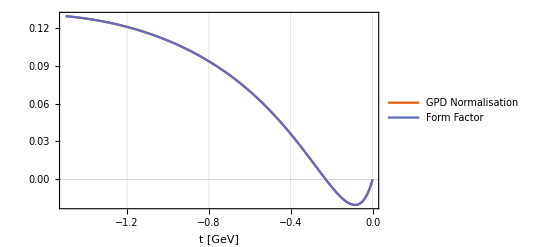

3.53468

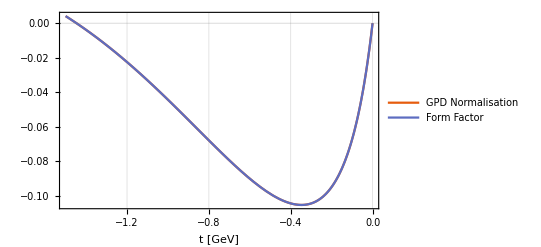

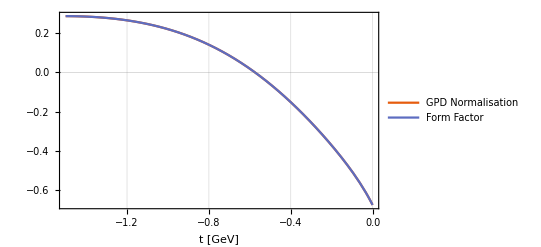

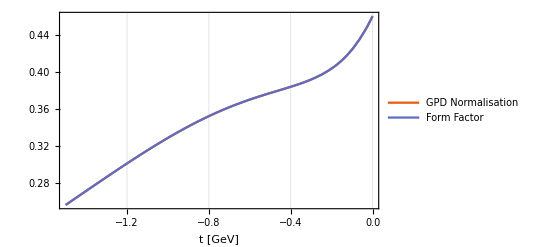

```mathematica
(* Construct the Helicity Amplitudes for MAID2007 & MAID2008 data *)
(* Parameters *)
αfs=0.0072973525643;
KinematicFactor[W_]:=(W^2-mN^2)/(2W);

Aα0p=-61.4*10^-3; (* All Units are GeV^n *)
Aa1p=0.871;
Aa2p=-3.516;
Aa3p=0;
Aa4p=-0.158;
Ab1p=1.36;
Sα0p=4.2*10^-3;
Sa1p=40.0;
Sa2p=0;
Sa3p=0;
Sa4p=1.50;
Sb1p=1.75;

Aα0n=54.1*10^-3;
Aa1n=0.95;
Aa2n=0;
Aa3n=0;
Aa4n=0;
Ab1n=1.77;
Sα0n=-41.5*10^-3;
Sa1n=2.98;
Sa2n=0;
Sa3n=0;
Sa4n=0;
Sb1n=1.55;

(* Helicity Amplitudes *)
HelicityAmplitudeAp[QSquared_]:=Aα0p(1+Aa1p*QSquared+Aa2p*QSquared^2+Aa3p*QSquared^3+Aa4p*QSquared^4)Exp[-Ab1p*QSquared];
HelicityAmplitudeSp[QSquared_]:=Sα0p(1+Sa1p*QSquared+Sa2p*QSquared^2+Sa3p*QSquared^3+Sa4p*QSquared^4)Exp[-Sb1p*QSquared];

HelicityAmplitudeAn[QSquared_]:=Aα0n(1+Aa1n*QSquared+Aa2n*QSquared^2+Aa3n*QSquared^3+Aa4n*QSquared^4)Exp[-Ab1n*QSquared];
HelicityAmplitudeSn[QSquared_]:=Sα0n(1+Sa1n*QSquared+Sa2n*QSquared^2+Sa3n*QSquared^3+Sa4n*QSquared^4)Exp[-Sb1n*QSquared];

QPlusSquared[QSquared_,W_]:=(mN+W)^2+QSquared;
QMinusSquared[QSquared_,W_]:=(mN-W)^2+QSquared;
NPlusMAID[QSquared_,W_]:=Sqrt[(π αfs QPlusSquared[QSquared,W])/(W*mN*KinematicFactor[W])];
NMinusMAID[QSquared_,W_]:=Sqrt[(π αfs QMinusSquared[QSquared,W])/(W*mN*KinematicFactor[W])];
kRMAID[QSquared_,W_]:=Sqrt[QPlusSquared[QSquared,W]QMinusSquared[QSquared,W]]/(2W);


(* Transition Form Factors *)

F1TransitionProton[QSquared_,W_]:=1/NMinusMAID[QSquared,W]*QSquared/QPlusSquared[QSquared,W]*(HelicityAmplitudeAp[QSquared]+(Sqrt[2](W+mN))/kRMAID[QSquared,W]*HelicityAmplitudeSp[QSquared]);
F2TransitionProton[QSquared_,W_]:=1/NMinusMAID[QSquared,W]*QSquared/QPlusSquared[QSquared,W]*((W+mN)^2/QSquared*HelicityAmplitudeAp[QSquared]-(Sqrt[2](W+mN))/kRMAID[QSquared,W]*HelicityAmplitudeSp[QSquared]);
F1TransitionNeutron[QSquared_,W_]:=1/NMinusMAID[QSquared,W]*QSquared/QPlusSquared[QSquared,W]*(HelicityAmplitudeAn[QSquared]+(Sqrt[2](W+mN))/kRMAID[QSquared,W]*HelicityAmplitudeSn[QSquared]);
F2TransitionNeutron[QSquared_,W_]:=1/NMinusMAID[QSquared,W]*QSquared/QPlusSquared[QSquared,W]*((W+mN)^2/QSquared*HelicityAmplitudeAn[QSquared]-(Sqrt[2](W+mN))/kRMAID[QSquared,W]*HelicityAmplitudeSn[QSquared]);



(*Flavor decomposition from p/n*)
F1uTransition[t_]:=2 F1TransitionProton[-t,mR]+F1TransitionNeutron[-t,mR];
F1dTransition[t_]:=2 F1TransitionNeutron[-t,mR]+F1TransitionProton[-t,mR];

F2uTransition[t_]:=2 F2TransitionProton[-t,mR]+F2TransitionNeutron[-t,mR];
F2dTransition[t_]:=2 F2TransitionNeutron[-t,mR]+F2TransitionProton[-t,mR];
(* These are the targets for the first moments of the transition flavor GPDs at any t *)

(* Unit-normalized transition shapes sU/sD (∫s=1) *)
sUTransition[β_]:=(β^(-α0) (1-β)^nU)/NIntegrate[β^(-α0) (1-β)^nU,{β,0,1}];
sDTransition[β_]:=(β^(-α0) (1-β)^nD)/NIntegrate[β^(-α0) (1-β)^nD,{β,0,1}];

(* Use the same profile function *)

(* slopes - set to the same for now: tunable later *)
bHuTransition=bHu;bHdTransition=bHd;
bEuTransition=bEu;bEdTransition=bEd;

(* t-dependent normalizations to enforce first moments *)
NormHu[b_][t_]:=NIntegrate[sUTransition[β]*tDepH[b][β,t],{β,0,1}]; 
NormHd[b_][t_]:=NIntegrate[sDTransition[β]*tDepH[b][β,t],{β,0,1}]; NormEu[b_][t_]:=NIntegrate[sUTransition[β]*tDepE[b][β,t],{β,0,1}]; 
NormEd[b_][t_]:=NIntegrate[sDTransition[β]*tDepE[b][β,t],{β,0,1}]; 

(* Flavor-dependent prefactors: divide out the slope integral so ∫H^q=F1qTR(t), ∫E^q=F2qTR(t) *)
CHuTransition[t_]:=F1uTransition[t]/NormHu[bHuTransition][t];
CHdTransition[t_]:=F1dTransition[t]/NormHd[bHdTransition][t];
CEuTransition[t_]:=F2uTransition[t]/NormEu[bEuTransition][t];
CEdTransition[t_]:=F2dTransition[t]/NormEd[bEdTransition][t];

(*DD kernels for transition*)
hUHTransition[β_,α_,t_]:=CHuTransition[t]*sUTransition[β]*profile[β,α];
hDHTransition[β_,α_,t_]:=CHdTransition[t]*sDTransition[β]*profile[β,α];
hUETransition[β_,α_,t_]:=CEuTransition[t]*sUTransition[β]*profile[β,α];
hDETransition[β_,α_,t_]:=CEdTransition[t]*sDTransition[β]*profile[β,α];

(*Transition flavor GPDs*)
H1UTransition[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hUHTransition,x,ξ,t,tDepH[bHuTransition]];
H1DTransition[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hDHTransition,x,ξ,t,tDepH[bHdTransition]];

E1UTransition[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hUETransition,x,ξ,t,tDepE[bEuTransition]];
E1DTransition[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hDETransition,x,ξ,t,tDepE[bEdTransition]];


(* Use Forward shortcut to avoid Numerical effects *)
H1UTransitionForward[x_,t_]:=CHuTransition[t]*sUTransition[x]*tDepH[bHuTransition][x,t];
H1DTransitionForward[x_,t_]:=CHdTransition[t]*sDTransition[x]*tDepH[bHdTransition][x,t];
E1UTransitionForward[x_,t_]:=CEuTransition[t]*sUTransition[x]*tDepE[bEuTransition][x,t];
E1DTransitionForward[x_,t_]:=CEdTransition[t]*sDTransition[x]*tDepE[bEdTransition][x,t];

(* Check Normalisations - plots should overlap *)
testH1uTransition[t_]:=NIntegrate[H1UTransitionForward[x,t],{x,0,1}];
testH1dTransition[t_]:=NIntegrate[H1DTransitionForward[x,t],{x,0,1}];
testE1uTransition[t_]:=NIntegrate[E1UTransitionForward[x,t],{x,0,1}];
testE1dTransition[t_]:=NIntegrate[E1DTransitionForward[x,t],{x,0,1}];
Plot[{testH1uTransition[t],F1uTransition[t]},{t,-1.5,0},
FrameLabel->{"t [GeV]",None},
PlotLegends->Placed[{"GPD Normalisation","Form Factor"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]
Plot[{testH1dTransition[t],F1dTransition[t]},{t,-1.5,0},
FrameLabel->{"t [GeV]",None},
PlotLegends->Placed[{"GPD Normalisation","Form Factor"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]
Plot[{testE1uTransition[t],F2uTransition[t]},{t,-1.5,0},
FrameLabel->{"t [GeV]",None},
PlotLegends->Placed[{"GPD Normalisation","Form Factor"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]
Plot[{testE1dTransition[t],F2dTransition[t]},{t,-1.5,0},
FrameLabel->{"t [GeV]",None},
PlotLegends->Placed[{"GPD Normalisation","Form Factor"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]
```

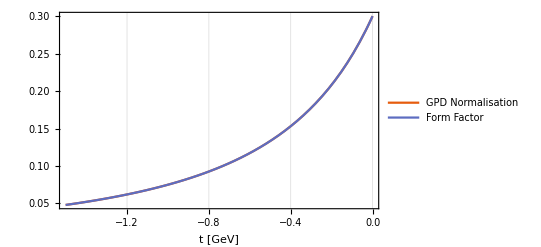

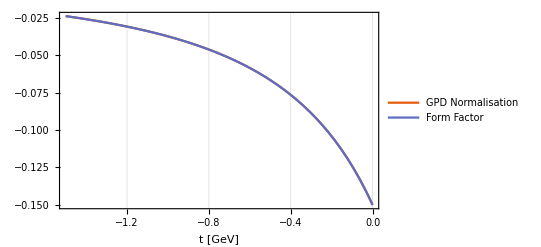

2.41218

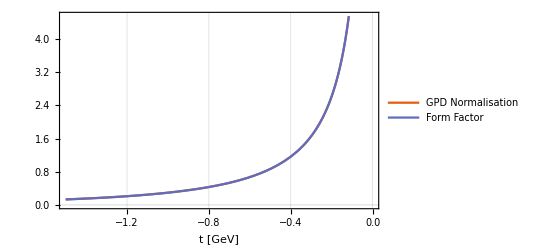

2.43436

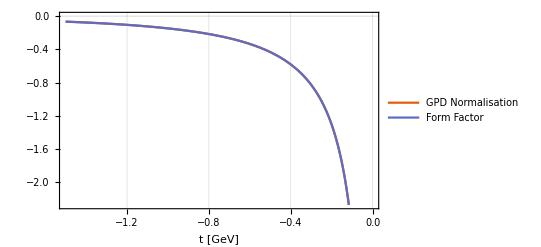

```mathematica
εGPcut=10^-3; GPmax=10^3;
Subscript[M, A]=1.0; (* Dipole Axial Mass in GeV *)
GA0p=0.25;GA0n=-0.20;
bPT=0.8;  (*GeV^{-2}:mild damping of the pole residue*)

GATransitionProton[t_]:=GA0p/((1-t/Subscript[M, A]^2)^2);
GATransitionNeutron[t_]:=GA0n/((1-t/Subscript[M, A]^2)^2);

GAuTransition[t_]:=2GATransitionProton[t]+GATransitionNeutron[t];
GAdTransition[t_]:=2GATransitionNeutron[t]+GATransitionProton[t];

GAu0=GAuTransition[0.];
GAd0=GAdTransition[0.];

gPiNRu=GAu0*(mR+mN)/(2 fπ);
gPiNRd=GAd0*(mR+mN)/(2 fπ);

GPuTransition[t_]:=(2 mN*fπ*gPiNRu)/(mπ^2-t)*Exp[bPT*t];
GPdTransition[t_]:=(2 mN*fπ*gPiNRd)/(mπ^2-t)*Exp[bPT*t];


(* Use the same profile function *)

(* slopes *)
bHuTildeTransition=1.1;bHdTildeTransition=1.1;   (*slopes for∼H_{u,d}*)
bEuTildeTransition=1.8;bEdTildeTransition=2.2;   (*slopes for∼E_{u,d} (often broader)*)


(* Flavor-dependent prefactors: divide out the slope integral so ∫H^q=F1qTR(t), ∫E^q=F2qTR(t) *)
(* We can use the same normalisation trick as for the non-axial case *)
CHuTildeTransition[t_]:=GAuTransition[t]/NormHu[bHuTildeTransition][t];
CHdTildeTransition[t_]:=GAdTransition[t]/NormHd[bHdTildeTransition][t];
CEuTildeTransition[t_]:=GPuTransition[t]/NormEu[bEuTildeTransition][t];
CEdTildeTransition[t_]:=GPdTransition[t]/NormEd[bEdTildeTransition][t];

(*DD kernels for transition*)
hUHTildeTransition[β_,α_,t_]:=CHuTildeTransition[t]*sUTransition[β]*profile[β,α];
hDHTildeTransition[β_,α_,t_]:=CHdTildeTransition[t]*sDTransition[β]*profile[β,α];
hUETildeTransition[β_,α_,t_]:=CEuTildeTransition[t]*sUTransition[β]*profile[β,α];
hDETildeTransition[β_,α_,t_]:=CEdTildeTransition[t]*sDTransition[β]*profile[β,α];

(*Transition flavor GPDs*)
tildeH1UTransition[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hUHTildeTransition,x,ξ,t,tDepH[bHuTildeTransition]];
tildeH1DTransition[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hDHTildeTransition,x,ξ,t,tDepH[bHdTildeTransition]];

tildeE1UTransition[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hUETildeTransition,x,ξ,t,tDepE[bEuTildeTransition]];
tildeE1DTransition[x_?NumericQ,ξ_?NumericQ,t_?NumericQ]:=DDint[hDETildeTransition,x,ξ,t,tDepE[bEdTildeTransition]];


(* Use Forward shortcut to avoid Numerical effects *)
tildeH1UTransitionForward[x_,t_]:=CHuTildeTransition[t]*sUTransition[x]*tDepH[bHuTildeTransition][x,t];
tildeH1DTransitionForward[x_,t_]:=CHdTildeTransition[t]*sDTransition[x]*tDepH[bHdTildeTransition][x,t];
tildeE1UTransitionForward[x_,t_]:=CEuTildeTransition[t]*sUTransition[x]*tDepE[bEuTildeTransition][x,t];
tildeE1DTransitionForward[x_,t_]:=CEdTildeTransition[t]*sDTransition[x]*tDepE[bEdTildeTransition][x,t];

(* Check Normalisations - plots should overlap *)
testH1uTildeTransition[t_]:=NIntegrate[tildeH1UTransitionForward[x,t],{x,0,1}];
testH1dTildeTransition[t_]:=NIntegrate[tildeH1DTransitionForward[x,t],{x,0,1}];
testE1uTildeTransition[t_]:=NIntegrate[tildeE1UTransitionForward[x,t],{x,0,1}];
testE1dTildeTransition[t_]:=NIntegrate[tildeE1DTransitionForward[x,t],{x,0,1}];
Plot[{testH1uTildeTransition[t],GAuTransition[t]},{t,-1.5,0},
FrameLabel->{"t [GeV]",None},
PlotLegends->Placed[{"GPD Normalisation","Form Factor"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]
Plot[{testH1dTildeTransition[t],GAdTransition[t]},{t,-1.5,0},
FrameLabel->{"t [GeV]",None},
PlotLegends->Placed[{"GPD Normalisation","Form Factor"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]
Plot[{testE1uTildeTransition[t],GPuTransition[t]},{t,-1.5,0},
FrameLabel->{"t [GeV]",None},
PlotLegends->Placed[{"GPD Normalisation","Form Factor"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]
Plot[{testE1dTildeTransition[t],GPdTransition[t]},{t,-1.5,0},
FrameLabel->{"t [GeV]",None},
PlotLegends->Placed[{"GPD Normalisation","Form Factor"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]
```

```mathematica
(* Isospin Symmetric GPDs *)
H1TransitionProton[x_,ξ_,t_]:=eu^2*H1UTransition[x,ξ,t]+ed^2*H1DTransition[x,ξ,t];
H1TransitionNeutron[x_,ξ_,t_]:=eu^2*H1DTransition[x,ξ,t]+ed^2*H1UTransition[x,ξ,t];

H2TransitionProton[x_,ξ_,t_]:=eu^2*E1UTransition[x,ξ,t]+ed^2*E1DTransition[x,ξ,t];
H2TransitionNeutron[x_,ξ_,t_]:=eu^2*E1DTransition[x,ξ,t]+ed^2*E1UTransition[x,ξ,t];

tildeH1TransitionProton[x_,ξ_,t_]:=eu^2*tildeH1UTransition[x,ξ,t]+ed^2*tildeH1DTransition[x,ξ,t];
tildeH1TransitionNeutron[x_,ξ_,t_]:=eu^2*tildeH1DTransition[x,ξ,t]+ed^2*tildeH1UTransition[x,ξ,t];

tildeH2TransitionProton[x_,ξ_,t_]:=eu^2*tildeE1UTransition[x,ξ,t]+ed^2*tildeE1DTransition[x,ξ,t];
tildeH2TransitionNeutron[x_,ξ_,t_]:=eu^2*tildeE1DTransition[x,ξ,t]+ed^2*tildeE1UTransition[x,ξ,t];
```

```mathematica
(* GPD Replacement Rules *)
ProtonTransitionGPDrr={H1->H1TransitionProton[xB,ξ/.BjorkenApprox[mN,mR],tMand],H2->H2TransitionProton[xB,ξ/.BjorkenApprox[mN,mR],tMand],
H1Tilde->tildeH1TransitionProton[xB,ξ/.BjorkenApprox[mN,mR],tMand],H2Tilde->tildeH2TransitionProton[xB,ξ/.BjorkenApprox[mN,mR],tMand]};
NeutronTransitionGPDrr={H1->H1TransitionNeutron[xB,ξ/.BjorkenApprox[mN,mR],tMand],H2->H2TransitionNeutron[xB,ξ/.BjorkenApprox[mN,mR],tMand],
H1Tilde->tildeH1TransitionNeutron[xB,ξ/.BjorkenApprox[mN,mR],tMand],H2Tilde->tildeH2TransitionNeutron[xB,ξ/.BjorkenApprox[mN,mR],tMand]};

ProtonGPDrr={H1->H1Proton[xB,ξ/.BjorkenApprox[mN,mN],tMand],
H2->H2Proton[xB,ξ/.BjorkenApprox[mN,mN],tMand],
H1Tilde->tildeH1Proton[xB,ξ/.BjorkenApprox[mN,mN],tMand],
H2Tilde->SetToZero}/.MForwardGPDrr/.ForwardMomCons;
NeutronGPDrr={H1->H1Neutron[xB,ξ/.BjorkenApprox[mN,mN],tMand],
H2->H2Neutron[xB,ξ/.BjorkenApprox[mN,mN]/.MTransitionGPDrr/.TransitionMomCons,tMand],
H1Tilde->tildeH1Neutron[xB,ξ/.BjorkenApprox[mN,mN],tMand],
H2Tilde->SetToZero}/.MForwardGPDrr/.ForwardMomCons;
(*ProtonGPDrr={H1->H1Proton[xB,ξ/.BjorkenApprox[mN,mN],tMand],
H2->H2Proton[xB,ξ/.BjorkenApprox[mN,mN],tMand],
H1Tilde->tildeH1Proton[xB,ξ/.BjorkenApprox[mN,mN],tMand],
H2Tilde->tildeH2Proton[xB,ξ/.BjorkenApprox[mN,mN],tMand]}/.MForwardGPDrr/.ForwardMomCons;
NeutronGPDrr={H1->H1Neutron[xB,ξ/.BjorkenApprox[mN,mN],tMand],
H2->H2Neutron[xB,ξ/.BjorkenApprox[mN,mN]/.MTransitionGPDrr/.TransitionMomCons,tMand],
H1Tilde->tildeH1Neutron[xB,ξ/.BjorkenApprox[mN,mN],tMand],
H2Tilde->tildeH2Neutron[xB,ξ/.BjorkenApprox[mN,mN],tMand]}/.MForwardGPDrr/.ForwardMomCons;*)
```

16.9438

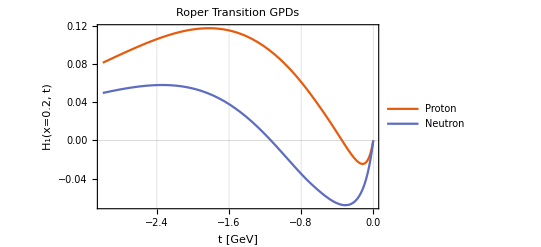

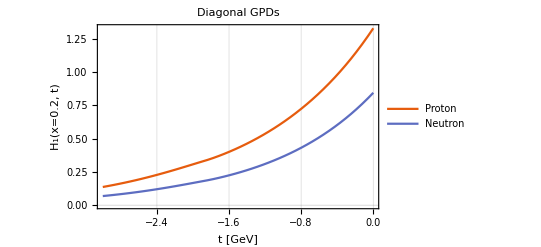

11.6552

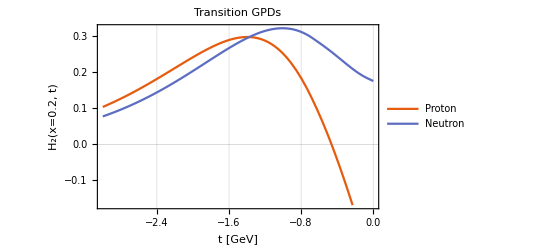

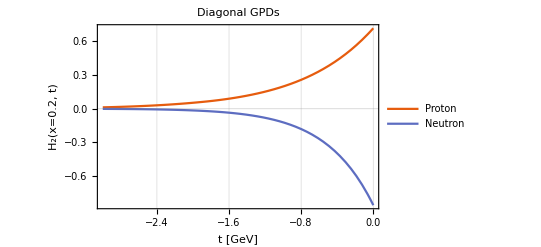

6.95654

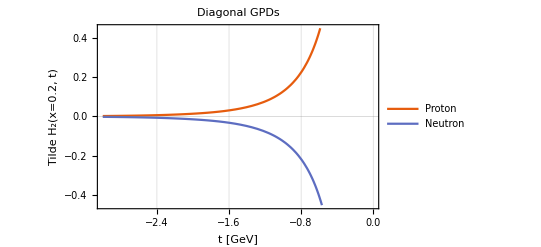

```mathematica
(*Plot the GPDs*)
Plot[{10^3 HelicityAmplitudeAp[QSquared],10^3 HelicityAmplitudeAn[QSquared]},{QSquared,0,6},
FrameLabel->{"Q^2 [GeV^2]","A_(1/2)(Q^2) [10^-3 GeV^(-1/2)]"},
PlotLabel->"Helicity Amplitude",
PlotLegends->Placed[{"Proton","Neutron"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{0,6},Automatic}];
Plot[{10^3 HelicityAmplitudeSp[QSquared],10^3 HelicityAmplitudeSn[QSquared]},{QSquared,0,6},
FrameLabel->{"Q^2 [GeV^2]","S_(1/2)(Q^2) [10^-3 GeV^(-1/2)]"},
PlotLabel->"Helicity Amplitude",
PlotLegends->Placed[{"Proton","Neutron"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{0,6},Automatic}];

Plot[{F1TransitionProton[QSquared,mR],F1TransitionNeutron[QSquared,mR]},{QSquared,0,6},
FrameLabel->{"Q^2 [GeV^2]","F_1(Q^2)"},
PlotLabel->"Transition Form Factors",
PlotLegends->Placed[{"Proton","Neutron"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{0,6},Automatic}];
Plot[{F2TransitionProton[QSquared,mR],F2TransitionNeutron[QSquared,mR]},{QSquared,0,6},
PlotLabel->"Transition Form Factors",
FrameLabel->{"Q^2 [GeV]","F_2(Q^2)"},
PlotLegends->Placed[{"Proton","Neutron"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{0,6},Automatic}];
Plot[{H1TransitionProton[xB,ξ/.BjorkenApprox[mN,mR],tMand]/.{xB->0.2},H1TransitionNeutron[xB,ξ/.BjorkenApprox[mN,mR],tMand]/.{xB->0.2}},{tMand,-3,0},
PlotLabel->"Roper Transition GPDs",
FrameLabel->{"t [GeV]","H_1(x=0.2, t)"},
PlotLegends->Placed[{"Proton","Neutron"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]
Plot[{H1Proton[xB,ξ/.BjorkenApprox[mN,mN],tMand]/.{xB->0.2},H1Neutron[xB,ξ/.BjorkenApprox[mN,mN],tMand]/.{xB->0.2}},{tMand,-3,0},
PlotLabel->"Diagonal GPDs",
FrameLabel->{"t [GeV]","H_1(x=0.2, t)"},
PlotLegends->Placed[{"Proton","Neutron"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]
(*Plot[H1nQuark[xB,ξ/.BjorkenApprox[mN,m3Quark],tMand]/.{xB->0.2},{tMand,-1.5,0},
PlotLabel->"3-Quark GPDs",
FrameLabel->{"t [GeV]","H_1(x=0.2, t)"},
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]*)
Plot[{H2TransitionProton[xB,ξ/.BjorkenApprox[mN,mR],tMand]/.{xB->0.2},H2TransitionNeutron[xB,ξ/.BjorkenApprox[mN,mR],tMand]/.{xB->0.2}},{tMand,-3,0},
PlotLabel->"Transition GPDs",
FrameLabel->{"t [GeV]","H_2(x=0.2, t)"},
PlotLegends->Placed[{"Proton","Neutron"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]
Plot[{H2Proton[xB,ξ/.BjorkenApprox[mN,mN],tMand]/.{xB->0.2},H2Neutron[xB,ξ/.BjorkenApprox[mN,mN],tMand]/.{xB->0.2}},{tMand,-3,0},
PlotLabel->"Diagonal GPDs",
FrameLabel->{"t [GeV]","H_2(x=0.2, t)"},
PlotLegends->Placed[{"Proton","Neutron"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]

(*Plot[{tildeH2Proton[xB,ξ/.BjorkenApprox[mN,mN],tMand]/.{xB->0.2},tildeH2Neutron[xB,ξ/.BjorkenApprox[mN,mN],tMand]/.{xB->0.2}},{tMand,-3,0},
PlotLabel->"Diagonal GPDs",
FrameLabel->{"t [GeV]","Tilde H_2(x=0.2, t)"},
PlotLegends->Placed[{"Proton","Neutron"},Top],
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{Automatic,0},Automatic}]*)
```

## Apply GPDs & Create ∑_spins |M|^2

```mathematica
(*Apply GPDs*)
If[TargetNucleonType=="Proton",
MRoperTransitionGPDSubbed=MRoperTransition/.ProtonTransitionGPDrr;
MRoperTransitionAdjointGPDSubbed=MRoperTransitionAdjoint/.ProtonTransitionGPDrr;
];

If[TargetNucleonType=="Neutron",
MRoperTransitionGPDSubbed=MRoperTransition/.NeutronTransitionGPDrr;
MRoperTransitionAdjointGPDSubbed=MRoperTransitionAdjoint/.NeutronTransitionGPDrr;
];


If[FinalNucleonType=="Proton",
MForwardTransitionGPDSubbed=MForwardTransition/.ProtonGPDrr;
MForwardTransitionAdjointGPDSubbed=MForwardTransitionAdjoint/.ProtonGPDrr;
];

If[FinalNucleonType=="Neutron",
MForwardTransitionGPDSubbed=MForwardTransition/.NeutronGPDrr;
MForwardTransitionAdjointGPDSubbed=MForwardTransitionAdjoint/.NeutronGPDrr;
];

(*MnQuarkTransitionGPDSubbed=MnQuarkTransition/.nQuarkGPDrr;
MnQuarkTransitionAdjointGPDSubbed=MnQuarkTransitionAdjoint/.nQuarkGPDrr;*)
```

```mathematica
ForwardHadronicTensor=1/2*SpinProjector[pF,mF,-BB,CC]*MForwardTransitionGPDSubbed*SpinProjector[p,mN,-FF,GG]*MForwardTransitionAdjointGPDSubbed;
RoperHadronicTensor=1/2*SpinProjector[pF,mF,-BB,CC]*MRoperTransitionGPDSubbed*SpinProjector[p,mN,-FF,GG]*MRoperTransitionAdjointGPDSubbed;
(*nQuarkHadronicTensor=1/2*SpinProjector[pF,mF,-BB,CC]*MnQuarkTransitionGPDSubbed*SpinProjector[p,mN,-FF,GG]*MnQuarkTransitionAdjointGPDSubbed;*)
ForwardRoperHadronicTensor=1/2*SpinProjector[pF,mF,-BB,CC]*(MForwardTransitionGPDSubbed+MRoperTransitionGPDSubbed)*SpinProjector[p,mN,-FF,GG]*(MForwardTransitionAdjointGPDSubbed+MRoperTransitionAdjointGPDSubbed);
(*ForwardnQuarkHadronicTensor=1/2*SpinProjector[pF,mF,-BB,CC]*(MForwardTransitionGPDSubbed+MnQuarkTransitionGPDSubbed)*SpinProjector[p,mN,-FF,GG]*(MForwardTransitionAdjointGPDSubbed+MnQuarkTransitionAdjointGPDSubbed);*)
```

## Some Shared xCoba CTensors

```mathematica
(* Vector to Extract p^0 Component *)
ECoba=CTensor[{1,0,0,0},{Mink}];

(************ Setup Components of Spinors and γ Matrices ************)
(* Convert Identity Matrix to Tensor *)
IdCoba=CTensor[IdentityMatrix[4],{-Mat,Mat}];

(* Set Up Gamma Matrices in Dirac Basis *)
γ0Mat = {{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}};
γ1Mat = {{0, 0, 0, 1}, {0, 0, 1, 0}, {0, -1, 0, 0}, {-1, 0, 0, 0}};
γ2Mat = {{0, 0, 0, -I}, {0, 0, I, 0}, {0, I, 0, 0}, {-I, 0, 0, 0}};
γ3Mat = {{0, 0, 1, 0}, {0, 0, 0, -1}, {-1, 0, 0, 0}, {0, 1, 0, 0}};
γ5Expansion = I*γ0Mat . γ1Mat . γ2Mat . γ3Mat;

(* γ Matrices as a Vector of Matrices *)
γVec={γ0Mat, γ1Mat,γ2Mat,γ3Mat};

(* Set Up Sigma Matrices in Dirac Basis *)
σ00 = {{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}};
σ11 = {{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}};
σ22 = {{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}};
σ33 = {{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}};

σ01 = I*γ0Mat . γ1Mat;
σ02 = I*γ0Mat . γ2Mat;
σ03 = I*γ0Mat . γ3Mat;

σ10 = -σ01;
σ12 = I*γ1Mat . γ2Mat;
σ13 = I*γ1Mat . γ3Mat;

σ20 = -σ02;
σ21 = -σ12;
σ23 = I*γ2Mat . γ3Mat;

σ30 = -σ03;
σ31 = -σ13;
σ32 = -σ23;

(* σ Matrices as a Matrix of Matrices *)
σMat = {{σ00, σ01, σ02, σ03}, {σ10, σ11, σ12, σ13}, {σ20, σ21, σ22, σ23}, {σ30, σ31, σ32, σ33}};


(* Convert γ and σ Matrices to Tensors *)
γ0Coba=CTensor[γ0Mat,{-Mat,Mat}];
γ5Coba=CTensor[γ5Expansion,{-Mat,Mat}];
γCoba=CTensor[γVec,{Mink,-Mat,Mat}];
σCoba = CTensor[σMat, {Mink, Mink, -Mat, Mat}];




(*Define the Levi-Civita symbol manually*)
LeviCivitaSymbol[indices__]:=Signature[{indices}];
LeviCivitaCoba=CTensor[Array[LeviCivitaSymbol,{4,4,4,4}],{Mink,Mink,Mink,Mink}];

(* Unit Spinor Components *)
spinorUp={1,0,0,0};
spinorDown={0,1,0,0};

spinorUpBar={1,0,0,0}.γ0Mat;
spinorDownBar={0,1,0,0}.γ0Mat;

(* Spinors as Tensors *)
spinorUpCoba=CTensor[spinorUp,{Mat}];
spinorDownCoba=CTensor[spinorDown,{Mat}];

spinorUpBarCoba=CTensor[spinorUpBar,{Mat}];
spinorDownBarCoba=CTensor[spinorDownBar,{Mat}];
```

## Some Testing

```mathematica
quickRR={γ->γCoba,Id->IdCoba,γ0->γ0Coba, γ5->γ5Coba, σ->σCoba,LeviCivita->LeviCivitaCoba, EVec->ECoba};
(* Should give 4I *)
γ[-μ,-AA,BB]γ[μ,-BB,CC]/.quickRR//Simplify;

(* Should give 2 η^μν I -- written as an array of 2I*{1,-1,-1,-1} *)
(γ[-μ,-AA,BB]γ[-ν,-BB,CC] + γ[-ν,-AA,BB]γ[-μ,-BB,CC]){CTensor[{1,0,0,0},{Mink}][ν],CTensor[{0,1,0,0},{Mink}][ν],CTensor[{0,0,1,0},{Mink}][ν],CTensor[{0,0,0,1},{Mink}][ν]}{CTensor[{1,0,0,0},{Mink}][μ],CTensor[{0,1,0,0},{Mink}][μ],CTensor[{0,0,1,0},{Mink}][μ],CTensor[{0,0,0,1},{Mink}][μ]}/.quickRR//Simplify;

(* Should give Subscript[γ, ν] -- written as an array of {Subscript[γ, 0],Subscript[γ, 1],Subscript[γ, 2],Subscript[γ, 3]} -- note lower indices and minus signs *)
γ[-μ,-AA,BB]γ[-ν,-BB,CC]γ[μ,-CC,DD]/(-2)*{CTensor[{1,0,0,0},{Mink}][ν],CTensor[{0,1,0,0},{Mink}][ν],CTensor[{0,0,1,0},{Mink}][ν],CTensor[{0,0,0,1},{Mink}][ν]}/.quickRR//Simplify;

(* Should give 4 η^νρ I *)
γ[μ,-AA,BB]γ[ν,-BB,CC]γ[ρ,-CC,DD]γ[-μ,-DD,EE]/.quickRR//Simplify;

(* Should give 4 η^μν *)
γ[μ,-AA,BB]γ[ν,-BB,AA]/.quickRR//Simplify;

(* Should give 0 *)
γ[μ,-AA,BB]γ[ν,-BB,CC]γ5[-CC,AA]/.quickRR//Simplify;
γ5[-AA,AA]/.quickRR//Simplify;


(* Should give 0 *)
{ConjugateTranspose[γ0Mat]-γ0Mat//MatrixForm,
ConjugateTranspose[γ1Mat]+γ1Mat//MatrixForm,
ConjugateTranspose[γ2Mat]+γ2Mat//MatrixForm,
ConjugateTranspose[γ3Mat]+γ3Mat//MatrixForm,
ConjugateTranspose[γ5Expansion]-γ5Expansion//MatrixForm};

(* Hermiticity in the sense of the Dirac inner product *)
(*Chop@ToCanonical@(Nπ[k,gARoper,-AA,BB]- NπDagger[k,gARoper,-AA,BB] )/.rr*)

(*Chop@ToCanonical@((γ0[-AA,BB] Sf[p,mN,-CC,DD,0] γ0[-DD,FF])-Conjugate[Sf[p,mN,-AA,FF,0]])/.rr;*)

(* Should give 1 *)
(* This test can only be run after "rr" is defined in the "Run Code" cell *)
(*pTilde[-μ] n[μ]/.GPDrr/.BjorkenInvar/.MForwardGPDrr//.ForwardMomCons/.rr
pTilde[-μ] n[μ]/.GPDrr/.BjorkenInvar/.MTransitionGPDrr//.TransitionMomCons/.rr
pTilde[-μ] n[μ]/.GPDrr/.BjorkenInvar/.MTransitionGPDrr//.TransitionMomCons/.rr*)

(* Ward Identities -- should be 0 *)
(*Chop@ToCanonical@PhotonTensor*qPrime[-β]/.{qPrime->qPrimeCoba}/.rr
Chop@ToCanonical@PhotonTensor*qPrime[-λ]/.{qPrime->qPrimeCoba}/.rr
Chop@ToCanonical@FullLeptonicTensor*q[-α]/.{q->qCoba}/.rr
Chop@ToCanonical@FullLeptonicTensor*q[-ρ]/.{q->qCoba}/.rr*)

(* Should gives m^2*I *)
(*p[μ]γ[-μ,-AA,BB]p[ν]γ[-ν,-BB,CC]/.rr//Simplify
mN^2
ke[μ]γ[-μ,-AA,BB]ke[ν]γ[-ν,-BB,CC]/.rr//Simplify
kePrime[μ]γ[-μ,-AA,BB]kePrime[ν]γ[-ν,-BB,CC]/.rr//Simplify
me^2*)
```

## Run Code

### Calculations

```mathematica
Output={};
ProgIter=0;
NoOfIters=nSamplesmπN*nSamplesθπ*nSamplesϕπ;
Print["Progress: ",ProgressIndicator[Dynamic[ProgIter/(3*NoOfIters)]]," ",Dynamic[DecimalForm[N[ProgIter/(3*NoOfIters)*100],4]],"% complete"]




(* DO LOOP FOR PLOTTING VARIABLE *)
Do[(* mπN *)

tempPrint1=PrintTemporary["Calculating M_πN = ",mπN];

(* Phase Space Factor *)
yDef=Q^2/(2mN*xB*Ee);

LeptonicPhaseSpace=1/(2π)^5(xB yDef^2)/(32 Q^4 Sqrt[1+(4 mN^2 xB^2)/Q^2])(* dQ^2 Subscript[dx, B] dt dϕ *);
HadronicPhaseSpace=1/(2π)Sqrt[Lambda[mπN^2,mN^2,mπ^2]]/(2 mπN^2)(* Subscript[dΩ, π]^* *);
phaseSpaceFactor=(1(*Subscript[dM, R]^2*))/(2π)LeptonicPhaseSpace*HadronicPhaseSpace;

JacobianForInvariantMass=2mπN (*1/Subscript[dM, R]*);

(**********************************)
(**********************************)
(* Set Up Vectors in chosen frame *)
(**********************************)
(**********************************)
EPrime=Ee-Q^2/(2mN*xB); 
θe = ArcCos[(Ee*EPrime - (Q^2/2+me^2))/(Sqrt[Ee^2-me^2]Sqrt[EPrime^2-me^2])];



(* Lab Frame Input-side Vectors *)
pVec = {mN, 0, 0, 0};

qVec={Ee-EPrime,0,0,Sqrt[(Ee-EPrime)^2+Q^2]};
keVec={Ee,(Sqrt[Ee^2-me^2]Sqrt[EPrime^2-me^2])/Sqrt[(Ee-EPrime)^2+Q^2] Sin[θe],0,((Ee^2-me^2)-Sqrt[Ee^2-me^2]Sqrt[EPrime^2-me^2]Cos[θe])/Sqrt[(Ee-EPrime)^2+Q^2]};
kePrimeVec=keVec-qVec;

keMag=Norm[keVec[[2;;]]];
kePrimeMag=Norm[kePrimeVec[[2;;]]];


(* γ^*R CoM frame with z pointing in qVec direction *)
(* Note that ϕ is preserved in boosts along z-axis *)
qVecStarMag=Sqrt[Lambda[W^2,mN^2,-Q^2]]/(2W);

EGammaStar=(W^2-mπN^2)/(2W);
cosθγStar=Clip[(((W^2-mN^2-Q^2)/(2W))EGammaStar+1/2(tMand+Q^2))/(qVecStarMag*EGammaStar),{-1,1}];
sinθγStar=Sqrt[1-cosθγStar^2];

qPrimeStarVec = {EGammaStar, EGammaStar*sinθγStar*Cos[ϕ], EGammaStar*sinθγStar*Sin[ϕ], EGammaStar*cosθγStar}//Simplify;

pRStarVec={W,0,0,0}-qPrimeStarVec;


(* Move all this work back to the lab frame by boosting *)
Rγβ=Sqrt[(Ee-EPrime)^2+Q^2]/(mN+Ee-EPrime);
RγLorentz=(mN+Ee-EPrime)/W;
EGamma=RγLorentz*EGammaStar(1+Rγβ*cosθγStar);
(* Lab Frame output-side vectors *)
qPrimeVecZ=RγLorentz*EGammaStar(Rγβ+cosθγStar);
qPrimeVecT=EGammaStar*sinθγStar;
qPrimeVec={EGamma,qPrimeVecT*Cos[ϕ],qPrimeVecT*Sin[ϕ],qPrimeVecZ};
pRVec = pVec+qVec-qPrimeVec//Simplify;


(*EGamma=-(tMand+Q^2)/(2(Ee-EPrime-(Sqrt[(Ee-EPrime)^2+Q^2]Cos[θγ])));*)
(*If[EGamma<=0,Throw["E_γ negative"]];*)


Umin=1/Sqrt[Lambda[mπN^2,mN^2,mπ^2]](2 mπN^2(mCut^2-mπ^2)/(W^2-mπN^2)-(mπN^2+mπ^2-mN^2));
If[Umin<-1,
Print["Clamping minimum θπ"];
Umin=-1;];
If[Umin>=1,
Print["No contribution"];
Return[0.0]];

tempPrint2=PrintTemporary["θπ_min: ",ArcCos[Umin]];


If[mπN^2<(mF+mπ)^2,Throw["W_R below Nπ threshold"]]; (* Threshold check for R->Nπ *)
If[Lambda[W^2,mN^2,-Q^2]<0,Throw["Lambda Function Imaginary"]];


(* Photon Polarization Vectors *)
(* Phase factor of Exp[ +- I ϕ] omitted *)
(*ϵpVec=1/Sqrt[2]{0, -Cos[θγ]Cos[ϕ]+I Sin[ϕ],-Cos[θγ]Sin[ϕ]-I Cos[ϕ],Sin[θγ]};
ϵmVec=-1/Sqrt[2]{0, -Cos[θγ]Cos[ϕ]-I Sin[ϕ],-Cos[θγ]Sin[ϕ]+I Cos[ϕ],Sin[θγ]};*)


CalcDiffCrossSection[tensorID_,θπ_,ϕπ_]:=Module[
{EPiStar,kStarMag,kRestVec,EFStar,pFRestVec,vR,vRMag,Lorentz,kBoostedVec,pFBoostedVec,
pCoba,pFBoostedCoba,keCoba,kePrimeCoba,kBoostedCoba,qCoba,qPrimeCoba,(*ϵpCoba,ϵmCoba,ϵpConjCoba,ϵmConjCoba,*)
rr,
FullPhotonTensor,FullLeptonicTensor,FullHadronicTensor,
SpinSummed,
dσ},

ProgIter=ProgIter+1;

(* Resonance Rest Frame - Pion Momentum *)
EPiStar=(mπN^2+mπ^2-mF^2)/(2mπN)//Simplify;
kStarMag=Sqrt[Lambda[mπN^2,mπ^2,mF^2]]/(2mπN);
kRestVec = {EPiStar,kStarMag*Sin[θπ]*Cos[ϕπ],kStarMag*Sin[θπ]*Sin[ϕπ],kStarMag*Cos[θπ]}//Simplify;


(* Resonance Rest Frame - Final Nucleon Momentum *)
EFStar = mπN-EPiStar;
pFRestVec = {EFStar,-kRestVec[[2]],-kRestVec[[3]],-kRestVec[[4]]}//Simplify;



(******************************************)
(******************************************)
(*Boost Necessary Vectors into Chosen Frame*)
(******************************************)
(******************************************)
(* Some vectors were easier to calculate in alternate frames. Now boost them back into the lab frame *)

(* Define the difference between frames by creating a boost velocity *)
vR = pRVec[[2;;]]/pRVec[[1]]//Simplify;
vRMag=Norm[vR];
If[vRMag>=1-10^-14,Throw["Unphysical Boost"]];

Lorentz=1/Sqrt[1-vRMag^2];


kBoostedVec=LorentzBoost[kRestVec, vR];
pFBoostedVec=LorentzBoost[pFRestVec, vR];


(************************************)
(************************************)
(* Check All Particles are On-Shell *)
(************************************)
(************************************)
(*checkOnShell[vec_,mass_]:=Module[
{E2=vec[[1]]^2,p2=Total[vec[[2;;]]^2]},
Abs[E2-p2-mass^2] < 10^-7
];

{"keVec on-shell"->checkOnShell[keVec,me],"kePrimeVec on-shell"->checkOnShell[kePrimeVec,me]};
{"qPrimeVec on-shell"->checkOnShell[qPrimeVec,0],"kBoostedVec on-shell"->checkOnShell[kBoostedVec,mπ],"pFBoostedVec on-shell"->checkOnShell[pFBoostedVec,mF]};*)



(************************)
(************************)
(* Set up xCoba Tensors *)
(************************)
(************************)
(* Momentum Vectors as Tensors *)
pCoba=CTensor[pVec,{Mink}];
pFBoostedCoba=CTensor[pFBoostedVec,{Mink}];
keCoba=CTensor[keVec,{Mink}];
kePrimeCoba=CTensor[kePrimeVec,{Mink}];
kBoostedCoba=CTensor[kBoostedVec,{Mink}];
qCoba=CTensor[qVec,{Mink}];
qPrimeCoba=CTensor[qPrimeVec,{Mink}];

(* Local Polarization Vectors as Tensors *)
(*ϵpCoba=CTensor[ϵpVec,{Mink}];
ϵmCoba=CTensor[ϵmVec,{Mink}];
ϵpConjCoba=CTensor[Conjugate[ϵpVec],{Mink}];
ϵmConjCoba=CTensor[Conjugate[ϵmVec],{Mink}];*)


(* Replacement Rules *)
(* Full list of replacement rules *)
rr=Dispatch[{p->pCoba,ke->keCoba,kePrime->kePrimeCoba,γ->γCoba,Id->IdCoba,γ0->γ0Coba, γ5->γ5Coba, σ->σCoba,LeviCivita->LeviCivitaCoba,EVec->ECoba,pF->pFBoostedCoba,k->kBoostedCoba,qPrime->qPrimeCoba,SetToZero->0}];


(* Apply Momentum Replacement Rules *)
FullPhotonTensor=PhotonTensor/.rr;
FullLeptonicTensor=LeptonicTensor/.rr;
FullHadronicTensor=Switch[tensorID,
1,ForwardHadronicTensor,
2,RoperHadronicTensor,
3,ForwardRoperHadronicTensor
]/.rr;

(*Cross Section Calculations*)
SpinSummed=FullHadronicTensor*FullLeptonicTensor*FullPhotonTensor;

dσ=GeV2toPb*JacobianForInvariantMass*phaseSpaceFactor*SpinSummed  (* OUTPUT OF MODULE *)
];


{Uvals,UWeights}=Transpose@GaussianQuadratureWeights[nSamplesθπ,Umin,1];
θπvals=ArcCos[Uvals];
ϕπvals=Subdivide[0,2π,nSamplesϕπ-1];
ϕπWeights=ConstantArray[(2π)/nSamplesϕπ,nSamplesϕπ];
(*Print[Uvals];
Print[θπvals];*)

GLIntegralForward=Chop@Total@Flatten@Table[UWeights[[i]]*ϕπWeights[[j]]*CalcDiffCrossSection[1,θπvals[[i]],ϕπvals[[j]]],{i,nSamplesθπ},{j,nSamplesϕπ}];
GLIntegralRoper=Chop@Total@Flatten@Table[UWeights[[i]]*ϕπWeights[[j]]*CalcDiffCrossSection[2,θπvals[[i]],ϕπvals[[j]]],{i,nSamplesθπ},{j,nSamplesϕπ}];
GLIntegralForwardRoper=Chop@Total@Flatten@Table[UWeights[[i]]*ϕπWeights[[j]]*CalcDiffCrossSection[3,θπvals[[i]],ϕπvals[[j]]],{i,nSamplesθπ},{j,nSamplesϕπ}];


Output=Append[Output,{GLIntegralForward,GLIntegralRoper,(*nQuarkdσ,*)GLIntegralForwardRoper(*,ForwardnQuarkdσ*)}];
(*NotebookDelete[tempPrint];*)

NotebookDelete[{tempPrint1,tempPrint2}];
,
{mπN,mπNvals}
]
Print["Done"]
```

Progress:  % complete

573.682

Done

```mathematica
(* Extract Output *)
dSigmaForward=Output[[;;,1]];
dSigmaRoper=Output[[;;,2]];
dSigmaForwardRoper=Output[[;;,3]];
```

### Plotting

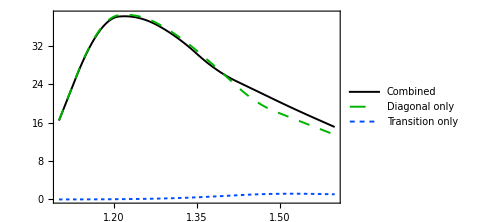

```mathematica
plotRoper=ListLinePlot[{dSigmaForwardRoper,dSigmaForward,dSigmaRoper},
InterpolationOrder->2,
DataRange->{mπNvals[[1]],mπNvals[[-1]]},
paperPlotOptions,
PlotStyle->{
{AbsoluteThickness[1.4],Black},
{AbsoluteThickness[1.4],RGBColor[0,0.7,0],Dashing[0.0225]},
{AbsoluteThickness[1.4],RGBColor[0,0.3,1],Dashing[0.007]}
},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{MaTeX["M_{\\pi N}~(\\mathrm{GeV})"],MaTeX["\\mathrm{d}\\sigma / \\mathrm{d}Q^2\\,\\mathrm{d}x_B\\,\\mathrm{d}t\\,\\mathrm{d}\\Phi\\,\\mathrm{d}M_{\\pi N}~(\\mathrm{pb/GeV}^5)"]},
PlotLegends->Placed[mainPlotLegend,{0.2,0.25}],
PlotRange->{{mπNvals[[1]],mπNvals[[-1]]},{0,Automatic}},
Epilog->Inset[MaTeX["-t = 1.5~\\mathrm{GeV}^2"],Scaled[{0.85,0.13}]]
]
(*plotTransitions=ListLinePlot[dSigmaRoper,
DataRange->{mπNvals[[1]],mπNvals[[-1]]},
InterpolationOrder->2,
FrameLabel->{"M_πN","dσ/..."},
PlotLabel->"Transition Term Only",
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,None},
PlotRange->{{mπNvals[[1]],mπNvals[[-1]]},{0,Automatic}},
Epilog->Inset[Style[Row[{"E_e = ",Ee,",  Q^2 = ",Q^2,",  x_B = ",xB,",  t = ",tMand,",  Φ = ",ϕ}],12,GrayLevel[0.35]],
Scaled[{0.5,0.25}]]
]
plotChange=ListLinePlot[(dSigmaForwardRoper-dSigmaForward)/dSigmaForward*100,
DataRange->{mπNvals[[1]],mπNvals[[-1]]},
InterpolationOrder->2,
FrameLabel->{"M_πN","dσ/....."},
PlotLabel->"% Change from Combination",
PlotLegends->{"Roper","qqq"},
PlotTheme->"Scientific",
Frame->True,
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->{Automatic,{0}},
PlotRange->{{mπNvals[[1]],mπNvals[[-1]]},{0,Automatic}},
Epilog->Inset[Style[Row[{"E_e = ",Ee,",  Q^2 = ",Q^2,",  x_B = ",xB,",  t = ",tMand,",  Φ = ",ϕ}],12,GrayLevel[0.35]],
Scaled[{0.5,0.25}]]
]*)
```

```mathematica
FileDirectory="/Users/mrumley02/Documents/meson-resonance-scattering-framework/images/";
FolderName=ToString[DateObject[][[1,1]]]<>"-"<>ToString[DateObject[][[1,2]]]<>"/x = "<>ToString[xB,InputForm]<>"/Q2 = "<>ToString[Q^2,InputForm]<>" GeV2/"<>"/t = "<>ToString[Round[tMand,0.01],InputForm]<>" GeV2/";
FileName="CrossSection "<>"FSI_DIPOLE_"<>TargetNucleonType <>"Pi"<>PionType<>"Type_"<>"["<>ToString[DateObject[][[1,1]]]<>"-"<>ToString[DateObject[][[1,2]]]<>"-"<>ToString[DateObject[][[1,3]]]<>"]";
FileExt=".pdf";

If[SaveResults==True,
Export[FileDirectory<>FolderName<>FileName<>FileExt,plotRoper,OverwriteTarget->"KeepBoth",ImageResolution->300];
(*Export[FileDirectory<>FolderName<>FileName<>"BothTransitions"<>FileExt,plotTransitions,OverwriteTarget->"KeepBoth",ImageResolution->300];*)
]
```